```mathematica
SetDirectory[NotebookDirectory[]];
rawData = Import["Segmented 2/3.json"];
meshData = Import["result.json"]
```

{points→{{200.,370.833},{173.958,359.375},{144.792,348.958},{159.375,384.375},{170.833,404.167},{179.167,426.042},{183.333,451.042},{188.542,467.708},{194.792,480.208},{205.208,498.958},{216.667,509.375},{235.417,505.208},{247.917,497.917},{264.583,484.375},{272.917,475.},{294.792,450.},{258.333,422.917},{235.417,404.167},{243.495,457.239},{228.751,479.421},{211.406,464.088}},elements→{{6,20,7},{3,2,1},{1,0,3},{3,0,4},{19,13,12},{17,5,4},{5,20,6},{20,5,17},{10,19,11},{18,20,17},{19,8,20},{0,17,4},{16,15,18},{8,19,9},{14,18,15},{18,19,20},{18,14,13},{9,19,10},{7,20,8},{13,19,18},{19,12,11},{18,17,16}}}

```mathematica
points ="points"/. meshData;
elements = "elements"/. meshData;
meshpoints = Map[points⟦#+1⟧&, elements];
```

```mathematica
coords = {};
"shapes"/. rawData;
AppendTo[coords, "points"/. #]&/@%;
```

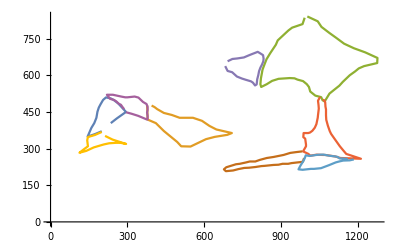

```mathematica
ListLinePlot[coords]
```

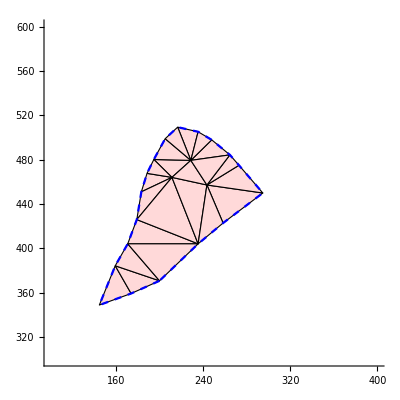

```mathematica
Show[ Graphics[{EdgeForm[Black],LightRed,Polygon/@meshpoints}],ListLinePlot[Append[coords⟦1⟧,coords⟦1,1⟧], PlotStyle->{Blue, Dashed}], PlotRange-> {{100,400}, {300,600}}, Axes-> True]
```

```mathematica
Polygon/@coords;
Area/@%
```

{10513.2,23293.7,78000.8,18145.1,11719.8,9165.5,7039.87,4635.55,7782.27}

```mathematica
Polygon/@meshpoints;
Total[Area/@%]
```

10513.2

199.966

199.966

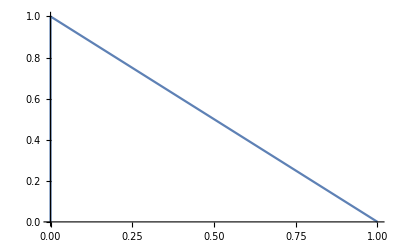

```mathematica
Total[Area[Polygon[meshpoints⟦1⟧]]]
0.5Abs[#⟦1,1⟧(#⟦2,2⟧-#⟦3,2⟧)+#⟦2,1⟧(#⟦3,2⟧-#⟦1,2⟧)+#⟦3,1⟧(#⟦1,2⟧-#⟦2,2⟧)]&@meshpoints⟦1⟧
```

{{1,0},{0,1},{0,0}}

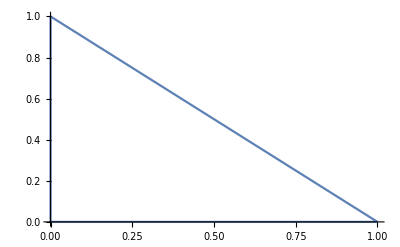

0.5

1/2

```mathematica
{{1,0}, {0,1}, {0,0}}
ListLinePlot[Append[#, First@#]&@%]
0.5Abs[(#⟦2⟧-#⟦1⟧).(#⟦3⟧-#⟦1⟧)]&@%%
Area[Polygon[%%%]]
```

{{1,0.5},{0,1},{0,0}}

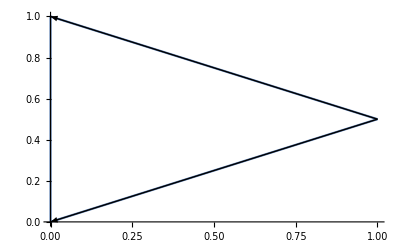

0.5

0.5

```mathematica
{{1,0.5}, {0,1}, {0,0}}
Show[ListLinePlot[Append[#, First@#]&@%],Graphics[{Arrow[{#⟦1⟧,#⟦2⟧}], Arrow[{#⟦1⟧,#⟦3⟧}]}&@%]]
0.5Abs[#⟦1,1⟧(#⟦2,2⟧-#⟦3,2⟧)+#⟦2,1⟧(#⟦3,2⟧-#⟦1,2⟧)+#⟦3,1⟧(#⟦1,2⟧-#⟦2,2⟧)]&@%%
Area[Polygon[%%%]]
```

```mathematica
{(#⟦2⟧-#⟦1⟧),#⟦3⟧-#⟦1⟧}&@{{1,0.5}, {0,1}, {0,0}}
```

{{-1,0.5},{-1,-0.5}}

{points→{{811.915,103.419},{799.094,97.4359},{780.291,97.4359},{778.581,114.53},{781.145,132.479},{787.128,147.009},{788.838,157.265},{788.838,179.487},{783.709,201.709},{779.436,213.675},{772.598,229.915},{764.051,244.444},{753.795,257.265},{736.701,270.085},{722.171,278.632},{705.932,284.615},{686.274,288.034},{677.726,296.581},{673.453,300.855},{674.308,321.368},{673.453,328.205},{664.906,333.333},{642.684,338.462},{606.786,345.299},{587.983,352.137},{576.017,357.265},{568.325,368.376},{629.863,373.504},{660.632,368.376},{672.598,373.504},{702.513,396.581},{714.479,403.419},{733.282,411.966},{768.325,436.752},{782.855,437.607},{795.675,449.573},{815.333,467.521},{823.026,484.615},{834.137,505.128},{835.846,516.239},{838.41,528.205},{841.829,549.573},{856.359,519.658},{891.402,505.983},{898.239,475.214},{900.803,464.103},{906.786,448.718},{915.333,420.513},{915.333,405.128},{912.769,389.744},{911.915,378.632},{905.077,370.085},{888.838,360.684},{858.068,344.444},{846.957,329.915},{836.701,310.256},{827.299,291.453},{820.462,270.085},{815.333,246.154},{808.496,215.385},{808.496,193.162},{806.786,182.051},{800.803,168.376},{798.239,141.88},{796.53,115.385},{687.102,310.23},{690.317,326.841},{681.325,351.011},{894.493,385.561},{599.094,370.94},{869.59,462.751},{777.892,398.038},{726.915,367.766},{888.505,412.821},{789.547,249.663},{717.624,312.939},{814.594,366.176},{817.682,413.143},{743.912,298.968},{785.413,293.079},{852.992,390.731}},elements→{{78,79,76},{46,45,70},{74,79,12},{67,72,30},{65,15,75},{76,72,78},{18,17,65},{15,65,16},{35,77,36},{17,16,65},{66,19,65},{70,36,77},{64,4,3},{14,78,75},{63,5,4},{5,63,6},{79,78,12},{10,59,74},{52,80,53},{59,9,8},{72,66,75},{46,73,47},{59,10,9},{64,3,2},{12,11,74},{69,23,27},{77,76,80},{27,23,22},{58,57,74},{76,71,72},{28,22,21},{24,69,25},{80,70,77},{25,69,26},{22,28,27},{67,28,21},{66,67,20},{67,21,20},{19,66,20},{65,19,18},{72,67,66},{29,28,67},{73,46,70},{33,32,71},{30,72,31},{71,34,33},{72,32,31},{23,69,24},{62,6,63},{55,76,79},{55,79,56},{64,2,1},{62,7,6},{7,61,60},{61,7,62},{59,8,60},{58,74,59},{1,0,64},{63,4,64},{12,78,13},{79,74,57},{78,14,13},{11,10,74},{73,70,80},{76,77,71},{68,80,52},{75,15,14},{32,72,71},{34,71,77},{55,54,76},{78,72,75},{30,29,67},{77,35,34},{57,56,79},{42,38,70},{38,37,70},{53,76,54},{53,80,76},{40,39,42},{42,41,40},{39,38,42},{73,80,68},{36,70,37},{66,65,75},{50,49,68},{73,48,47},{51,68,52},{70,43,42},{44,70,45},{68,48,73},{43,70,44},{49,48,68},{50,68,51},{60,8,7}}}

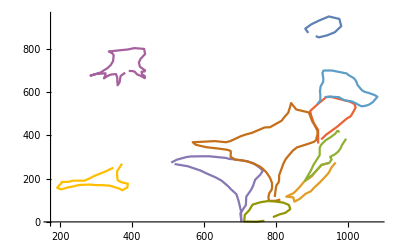

-Graphics-

```mathematica
SetDirectory[NotebookDirectory[]];
rawData1 = Import["Segmented 2/pepe3 10mcl - Aocul - 20Xspec.json"];
meshData1 = Import["resultpepe3.json"]
points1 ="points"/. meshData1;
elements1 = "elements"/. meshData1;
meshpoints1 = Map[points1⟦#+1⟧&, elements1];
coords1 = {};
"shapes"/. rawData1;
AppendTo[coords1, "points"/. #]&/@%;
ListLinePlot[coords1]
Import["cell granularity/pepe3 10mcl - Aocul - 20Xspec.jpg"]
```

```mathematica
meshpoints1
```

{{{910.417,859.375},{918.75,853.125},{925.107,870.282}},{{925.107,870.282},{941.667,862.5},{963.542,877.083}},{{881.25,893.75},{889.583,873.958},{897.917,913.542}},{{889.583,873.958},{910.417,859.375},{925.107,870.282}},{{889.583,873.958},{925.107,870.282},{897.917,913.542}},{{918.75,853.125},{941.667,862.5},{925.107,870.282}},{{925.107,870.282},{963.542,877.083},{919.792,931.25}},{{919.792,931.25},{963.542,877.083},{981.25,905.208}},{{981.25,905.208},{946.875,950.},{919.792,931.25}},{{946.875,950.},{981.25,905.208},{976.042,938.542}},{{919.792,931.25},{897.917,913.542},{925.107,870.282}}}

6

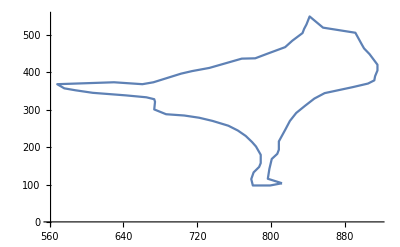

```mathematica
i = 6
ListLinePlot[Append[coords1⟦i⟧,coords1⟦i,1⟧]]
```

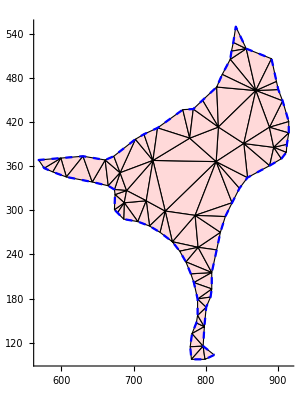

```mathematica
Show[ Graphics[{EdgeForm[Black],LightRed,Polygon/@meshpoints1}],ListLinePlot[Append[coords1⟦6⟧,coords1⟦6,1⟧], PlotStyle->{Blue, Dashed}] , Axes-> True]
```

```mathematica
Polygon/@coords1;
Area/@%
```

{6034.07,6506.08,7533.02,14389.3,23375.6,44351.7,14915.3,7922.78,10589.3,8292.98}